Import gluon spectral function

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<gluSpecMu0.mx
```

```mathematica
DumpSave["gluSpecMu0.mx",gluSpec];
```

Plot it

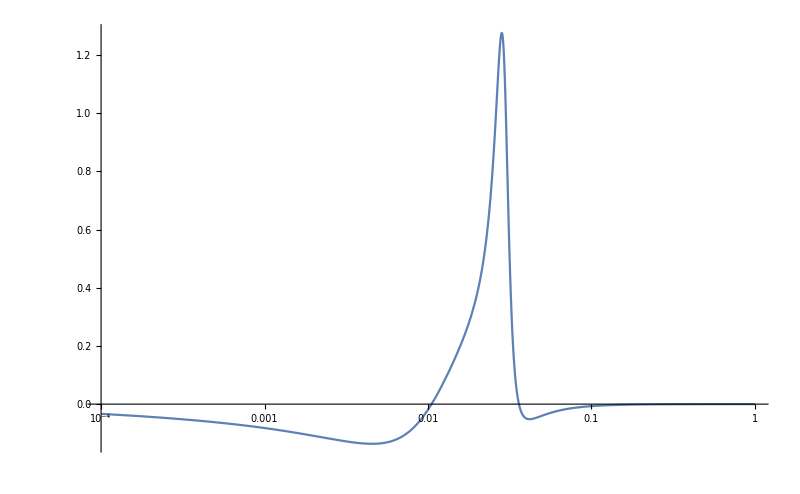

```mathematica
LogLinearPlot[gluSpec,{λ,10^-4,10^-0},ImageSize->800,PlotRange->All]
```

Evaluate object

```mathematica
gluSpec
```

Piecewise[{{-1.12791 (λ^2)^(-1+1/49 (93-√1201)), λ<1/(10000 10^(4/99))}, {2 Im[1/(0.120741-λ^2+1/24 (-InterpolatingFunction[…][λ]-InterpolatingFunction[…][λ]))], λ≥1/(10000 10^(4/99))}, {0, True}}]

Define as new function

```mathematica
gluSpecFunc[λ_]:=Evaluate[gluSpec]
```

Now you can plot the spectral function as a function of any argument

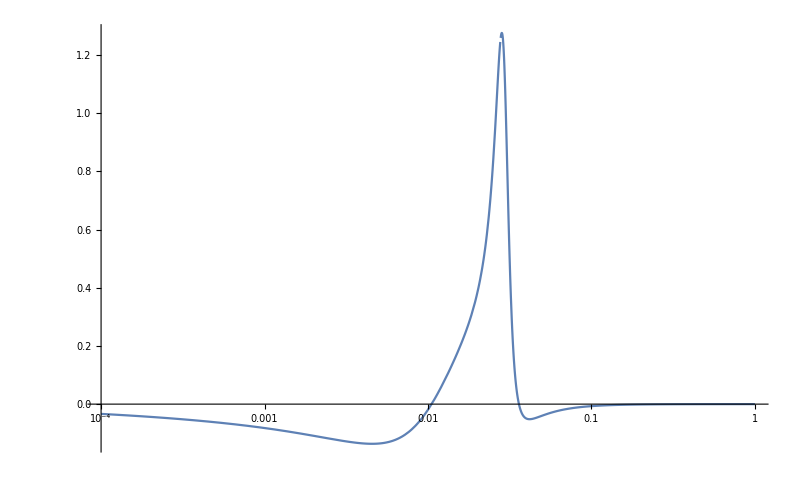

```mathematica
LogLinearPlot[gluSpecFunc[ω],{ω,10^-4,10^-0},ImageSize->800,PlotRange->All]
```